```mathematica
Quit
```

```mathematica
Needs["FunctionApproximations`"];
Needs["DifferentialEquations`NDSolveProblems`"];
```

```mathematica
Needs["ErrorBarPlots`"]
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Deriving the growth rate equation

### Deriving equation in δ:

#### Deriving in terms of conformal time

```mathematica
κ1 = ℋ'[η]/ℋ''[η];
κ2 = ℋ''[η]/ℋ'''[η];
```

```mathematica
coeffDelta = ((fR[t])^5(κ1-1)(2κ1-κ2)-16/a[η]^8 fRR[t]^4(κ2-2)k^8 ρ[t])/((fR[t])^5(κ1-1) + 24/a[η]^8 fRR[t]^4(fR[t])(κ2-2)k^8);
```

```mathematica
coeffDeltaQS= -(1+4 k^2/a[t]^2 fRR[t]/fR[t])/(1+3 k^2/a[t]^2 fRR[t]/fR[t])(ρ[t] a[t]^2)/(2fR[t]);
```

```mathematica
deltaDE = δ''[η] + ℋ[η]δ'[η]+coeffDeltaQS δ[η]==0
```

-(a[t]^2 (1+(4 k^2 fRR[t])/(a[t]^2 fR[t])) δ[η] ρ[t])/(2 fR[t] (1+(3 k^2 fRR[t])/(a[t]^2 fR[t])))+ℋ[η] δ'[η]+δ''[η]==0

#### Rewriting growth rate eqn in terms of coordinate time

```mathematica
timeReplacements = {ℋ[η]-> a[t]H[t],
ℋ'[η]-> a[t]^2(H[t]^2+H'[t]), 
ℋ''[η]-> a[t]^3(2 H[t]^3+4H[t]H'[t] + H''[t]),
ℋ'''[η]-> a[t]^4(6 H[t]^4 + 18 H[t]^2 H'[t] + 7H[t]H''[t] + 4 H'[t]^2+ H'''[t]),
δ[η]->δ[t],
δ'[η]->a[t]δ'[t],
δ''[η]->a[t]^2(H[t]δ'[t]+δ''[t])};
```

```mathematica
deltaDE = deltaDE/.timeReplacements //Simplify
```

1/2 a[t]^2 (-((a[t]^2 fR[t]+4 k^2 fRR[t]) δ[t] ρ[t])/(fR[t] (a[t]^2 fR[t]+3 k^2 fRR[t]))+4 H[t] δ'[t]+2 δ''[t])==0

```mathematica
deltaDELHS=With[
{expr=(deltaDE[[1]]-deltaDE[[2]])/. timeReplacements//FullSimplify},

expr/Coefficient[expr,δ''[t]]//FullSimplify
]
```

-((a[t]^2 fR[t]+4 k^2 fRR[t]) δ[t] ρ[t])/(2 fR[t] (a[t]^2 fR[t]+3 k^2 fRR[t]))+2 H[t] δ'[t]+δ''[t]

#### Using Same as Kelly’s

```mathematica
(*Kelly's*)
coeffDeltaQS = (-ρ[t])/(2fR[t])((1+4 fRR[t]/fR[t] k^2/a[t]^2)/(1+3 fRR[t]/fR[t] k^2/a[t]^2))
deltaDELHS = δ''[t] + 2H[t]δ'[t]+coeffDeltaQS δ[η]
```

-((1+(4 k^2 fRR[t])/(a[t]^2 fR[t])) ρ[t])/(2 fR[t] (1+(3 k^2 fRR[t])/(a[t]^2 fR[t])))

-((1+(4 k^2 fRR[t])/(a[t]^2 fR[t])) δ[η] ρ[t])/(2 fR[t] (1+(3 k^2 fRR[t])/(a[t]^2 fR[t])))+2 H[t] δ'[t]+δ''[t]

#### Rewriting growth rate eqn terms of cosmography

```mathematica
deltaDELHS
```

-((1+(4 k^2 fRR[t])/(a[t]^2 fR[t])) δ[η] ρ[t])/(2 fR[t] (1+(3 k^2 fRR[t])/(a[t]^2 fR[t])))+2 H[t] δ'[t]+δ''[t]

```mathematica
deltaDEcosmo=deltaDELHS/.{fRR[t]->fR[t] H[t] x[t]/R'[t]}//Simplify
```

-(δ[η] ρ[t] (4 k^2 H[t] x[t]+a[t]^2 R'[t]))/(2 fR[t] (3 k^2 H[t] x[t]+a[t]^2 R'[t]))+2 H[t] δ'[t]+δ''[t]

```mathematica
deltaDEcosmo=deltaDEcosmo/.{fR[t]->ρ[t]/(3 H[t]^2 Ω[t])}//Simplify
```

-(3 H[t]^2 δ[η] Ω[t] (4 k^2 H[t] x[t]+a[t]^2 R'[t]))/(6 k^2 H[t] x[t]+2 a[t]^2 R'[t])+2 H[t] δ'[t]+δ''[t]

```mathematica
deltaDEcosmo=deltaDEcosmo/.{R'[t]->6 H[t]^3(j[t]-q[t]-2)}//Simplify
```

-(H[t]^2 (3 a[t]^2 H[t]^2 (-2+j[t]-q[t])+2 k^2 x[t]) δ[η] Ω[t])/(2 a[t]^2 H[t]^2 (-2+j[t]-q[t])+k^2 x[t])+2 H[t] δ'[t]+δ''[t]

```mathematica
deltaDEcosmo//Simplify
```

-(H[t]^2 (3 a[t]^2 H[t]^2 (-2+j[t]-q[t])+2 k^2 x[t]) δ[η] Ω[t])/(2 a[t]^2 H[t]^2 (-2+j[t]-q[t])+k^2 x[t])+2 H[t] δ'[t]+δ''[t]

#### Rewriting growth rate eqn terms of redshift

```mathematica
δ'[t]=-(1+z)H[z]δ'[z];
δ''[t]=-(1+z)H[z]D[δ'[t],z];
δ[t]=δ[z];
```

```mathematica
a[t]=1/(1+z);
```

```mathematica
deltaDEcosmo//Simplify
```

-(H[t]^2 (3 H[t]^2 (-2+j[t]-q[t])+2 k^2 (1+z)^2 x[t]) δ[η] Ω[t])/(2 H[t]^2 (-2+j[t]-q[t])+k^2 (1+z)^2 x[t])-2 (1+z) H[t] H[z] δ'[z]+(1+z) H[z] ((1+z) H'[z] δ'[z]+H[z] (δ'[z]+(1+z) δ''[z]))

```mathematica
deltaDEcosmoz=deltaDEcosmo/.t->z/.η->z//Simplify
```

H[z] (-(H[z] (3 H[z]^2 (-2+j[z]-q[z])+2 k^2 (1+z)^2 x[z]) δ[z] Ω[z])/(2 H[z]^2 (-2+j[z]-q[z])+k^2 (1+z)^2 x[z])-2 (1+z) H[z] δ'[z]+(1+z) ((1+z) H'[z] δ'[z]+H[z] (δ'[z]+(1+z) δ''[z])))

```mathematica
NormaliseFactor =Coefficient[deltaDEcosmoz, δ''[z]]
(*NormaliseFactor=1*)
```

H[z] (H[z]+2 z H[z]+z^2 H[z])

```mathematica
dustODE[z_]=Simplify[ Coefficient[deltaDEcosmoz, δ[z]]/NormaliseFactor]δ[z]+ Simplify[ Coefficient[deltaDEcosmoz, δ'[z]]/NormaliseFactor]δ'[z]+Simplify[ Coefficient[deltaDEcosmoz, δ''[z]]/NormaliseFactor]δ''[z]==0
```

-((3 H[z]^2 (-2+j[z]-q[z])+2 k^2 (1+z)^2 x[z]) δ[z] Ω[z])/(2 (1+z)^2 H[z]^2 (-2+j[z]-q[z])+k^2 (1+z)^4 x[z])+(-1/(1+z)+H'[z]/H[z]) δ'[z]+δ''[z]==0

```mathematica
H[z_] = h[z]/H0;
k = κ/H0;
```

```mathematica
dustODE[z_]=dustODE[z]//Simplify
```

(-1/(1+z)+h'[z]/h[z]) δ'[z]+δ''[z]==((3 h[z]^2 (-2+j[z]-q[z])+2 (1+z)^2 κ^2 x[z]) δ[z] Ω[z])/(2 (1+z)^2 h[z]^2 (-2+j[z]-q[z])+(1+z)^4 κ^2 x[z])

## Solving for the matter density

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

```mathematica
(*Bella's values*)
qi = -0.647;
ji=1.035;
```

```mathematica
ϵ0=0;
ϵ1=(ji-1)/(3(qi+1));
ϵ2=ji-1;
ϵ3=(ji-1)/(3(qi-1/2));
```

#### kvals

```mathematica
kvals={0.01h, 0.02h, 0.03h, 0.04h, 0.05h, 0.1h, 0.2h}
```

{0.01 h,0.02 h,0.03 h,0.04 h,0.05 h,0.1 h,0.2 h}

```mathematica
𝓀vals=(3*10^5)/(100h)kvals;
```

### Solving module

```mathematica
SolvePerturbation[bgSol_Association,jModel_,ϵval_,kval_]:=
Module[{hf,xf,Ωf,qf,jf,ics,sol,replacements,𝓀val},
(*z0=bgSol["z0"];*)
hf=bgSol["h"];
xf=bgSol["x"];
Ωf=bgSol["Ω"];
qf=bgSol["q"];
𝓀val=(3*10^5)/(100h)kval;

replacements = {h->hf, x->xf, Ω->Ωf, q->qf, j[z]->jModel, κ->𝓀val, ϵ->ϵval};
(*ics = {δ[zinitial]==1/(1+zinitial),δ'[zinitial]==-1/(1+zinitial)^2};*)
ics = {δ[zinitial]==10^-5,δ'[zinitial]==0};

sol=NDSolve[{dustODE[z]/.replacements/.replacements,ics},δ,{z,zinitial,0}, PrecisionGoal->MachinePrecision][[1]];
<|"δ"->(δ/. sol),"zi"->zinitial|>];
```

### Models solutions

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Background solutions"];Get["BackgroundSols_model0.mx"];
Get["BackgroundSols_model1.mx"];
Get["BackgroundSols_model2.mx"];
Get["BackgroundSols_model3.mx"];
Get["BackgroundSols_LCDM.mx"];
```

```mathematica
z0=sol0["z0"]
zinitial=sol0["zinitial"]
```

6

2000

```mathematica
(*(*Solve each model*)
pertSol0=SolvePerturbation[sol0,j0[z],ϵ0,𝓀val];
pertSol1=SolvePerturbation[sol1,j1[z],ϵ1,𝓀val];
pertSol2=SolvePerturbation[sol2,j2[z],ϵ2,𝓀val];
pertSol3=SolvePerturbation[sol3,j3[z],ϵ3,𝓀val];*)
```

```mathematica
pertSols0=Association[Table[kval->SolvePerturbation[sol0,j0[z],ϵ0,kval],{kval,kvals}]];
```

```mathematica
pertSols3=Association[Table[kval->SolvePerturbation[sol3,j3[z],ϵ3,kval],{kval,kvals}]];
```

```mathematica
(*pertSols1=Association[Table[kval->SolvePerturbation[sol1,j1[z],ϵ1,kval],{kval,kvals}]];
pertSols2=Association[Table[kval->SolvePerturbation[sol2,j2[z],ϵ2,kval],{kval,kvals}]];
pertSols3=Association[Table[kval->SolvePerturbation[sol3,j3[z],ϵ3,kval],{kval,kvals}]];*)
```

#### LCDM:

```mathematica
(* ΛCDM parameters *)
Ωm0=0.3;   
ΩΛ0=1-Ωm0;
hLCDM[z_]:= Sqrt[Ωm0 (1+z)^3+ΩΛ0];
HLCDM[z_]=H0 hLCDM[z];
qLCDM[z_]:=-1+(1+z)HLCDM'[z]/HLCDM[z]
xLCDM[z_]:=0 
ΩLCDM[z_]:= (Ωm0(1+z)^3)/(Ωm0(1+z)^3+ΩΛ0)
```

```mathematica
LCDMreplacements={h[z]->hLCDM[z],h'[z]->hLCDM'[z], q[z]->qLCDM[z], j[z]->1, x[z]->xLCDM[z], Ω[z]->ΩLCDM[z]};
```

```mathematica
(*ics = {δ[zinitial]==1/(1+zinitial),δ'[zinitial]==-1/(1+zinitial)^2};*)
ics = {δ[zinitial]==10^-5,δ'[zinitial]==0};
LCDMsol=NDSolve[{dustODE[z]/.LCDMreplacements/.LCDMreplacements,ics},δ,{z,zinitial,0}, PrecisionGoal->MachinePrecision][[1]];
```

### Density Contrast solution:

#### Plotting δ model 0

```mathematica
colour={RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3],RGBColor[0.8,0.2,0.8],RGBColor[0.5,0.9,0.5],RGBColor[0.9,0.6,0.3]};
```

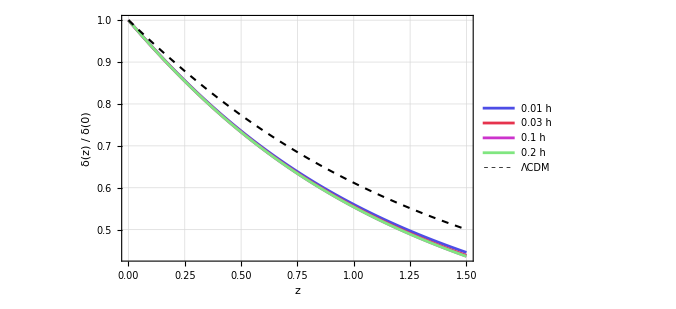

```mathematica
(*Plot δ(z) for all k values*)
kvalsDeltaPlot={0.01h, 0.03h, 0.1h,0.2h};
colour={RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3],RGBColor[0.8,0.2,0.8],RGBColor[0.5,0.9,0.5]};

δPlot0=Plot[
{Evaluate[Table[pertSols0[kval]["δ"][z]/pertSols0[kval]["δ"][0],{kval,kvalsDeltaPlot}]],LCDMsol[[1,2]][z]/LCDMsol[[1,2]][0]},{z,0,1.5},
PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvalsDeltaPlot],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.85,0.65}],FrameLabel->{"z","δ(z) / δ(0)"},PlotRange->All,Frame->True,GridLines->Automatic,ImageSize->500, PlotRangePadding->{None,Scaled[.05]}]

Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model0/QSdensityplot.png",δPlot0];
```

{0.01 h,0.02 h,0.03 h,0.04 h,0.05 h}

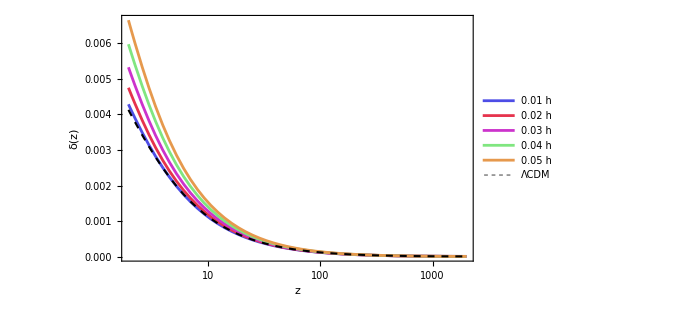

```mathematica
(*Plot δ(z) for all k values*)
kvals={0.01h, 0.02h, 0.03h, 0.04h, 0.05h}
colour={RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3],RGBColor[0.8,0.2,0.8],RGBColor[0.5,0.9,0.5],RGBColor[0.9,0.6,0.3]};
δPlot=LogLinearPlot[
{Evaluate[Table[pertSols0[kval]["δ"][z],{kval,kvals}]],LCDMsol[[1,2]][z]},{z,0,zinitial},
PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.85,0.65}],FrameLabel->{"z","δ(z)"},PlotRange->All,Frame->True,GridLines->Automatic,ImageSize->500, PlotRangePadding->{None, Scaled[.05]}]
```

#### Plotting δ model 3

```mathematica
colour={RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3],RGBColor[0.8,0.2,0.8],RGBColor[0.5,0.9,0.5],RGBColor[0.9,0.6,0.3]};
```

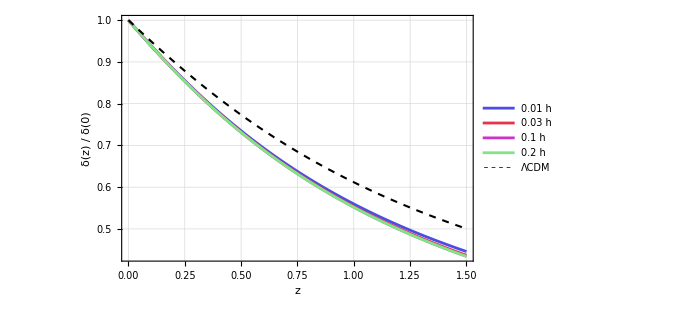

```mathematica
(*Plot δ(z) for all k values*)
kvalsDeltaPlot={0.01h, 0.03h, 0.1h,0.2h};
colour={RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3],RGBColor[0.8,0.2,0.8],RGBColor[0.5,0.9,0.5]};

δPlot3=Plot[
{Evaluate[Table[pertSols3[kval]["δ"][z]/pertSols3[kval]["δ"][0],{kval,kvalsDeltaPlot}]],LCDMsol[[1,2]][z]/LCDMsol[[1,2]][0]},{z,0,1.5},
PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvalsDeltaPlot],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.85,0.65}],FrameLabel->{"z","δ(z) / δ(0)"},PlotRange->All,Frame->True,GridLines->Automatic,ImageSize->500, PlotRangePadding->{None,Scaled[.05]}]

Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model3/QSdensityplot.png",δPlot3];
```

```mathematica
(*Plot δ(z) for all k values*)
kvals={0.01h, 0.02h, 0.03h, 0.04h, 0.05h}
colour={RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3],RGBColor[0.8,0.2,0.8],RGBColor[0.5,0.9,0.5],RGBColor[0.9,0.6,0.3]};
δPlot=LogLinearPlot[
{Evaluate[Table[pertSols0[kval]["δ"][z],{kval,kvals}]],LCDMsol[[1,2]][z]},{z,0,zinitial},
PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.85,0.65}],FrameLabel->{"z","δ(z)"},PlotRange->All,Frame->True,GridLines->Automatic,ImageSize->500, PlotRangePadding->{None, Scaled[.05]}]
```

{0.01 h,0.02 h,0.03 h,0.04 h,0.05 h}

-Graphics-

### Determining growth factor - growth index approximation

#### Growth rate function f

```mathematica
f[z_]=- (1+z)δ'[z]/δ[z];
```

```mathematica
f0[kval_,z_] := f[z]/.{δ->pertSols0[kval]["δ"]} ;
f3[kval_,z_] := f[z]/.{δ->pertSols3[kval]["δ"]} ;
fLCDM[z_] = f[z]/.{δ->LCDMsol[[1,2]]} ;
```

```mathematica
kvals={0.01h, 0.02h, 0.03h, 0.04h, 0.05h};
colour={RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3],RGBColor[0.8,0.2,0.8],RGBColor[0.5,0.9,0.5],RGBColor[0.9,0.6,0.3]};
```

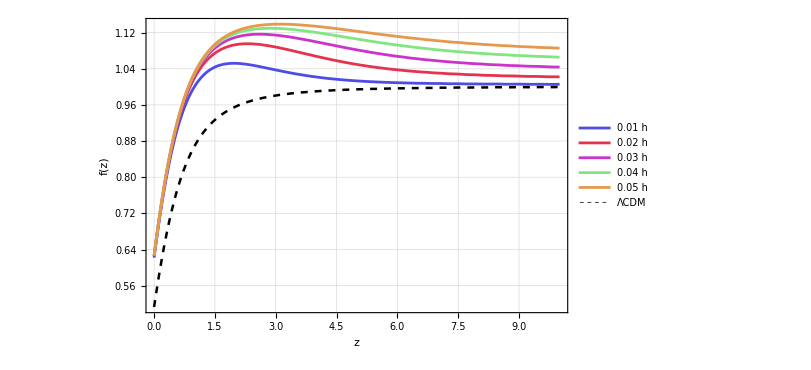

```mathematica
f0Plot=Plot[
{Evaluate[Table[f0[kval,z],{kval,kvals}]], fLCDM[z]},{z,0,10},PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],FrameLabel->{"z","f(z)"},PlotRange->All,Frame->True,ImageSize->600,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed], PlotRangePadding->{None, Scaled[.05]}]

Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model0/f0Plot.png",f0Plot];
```

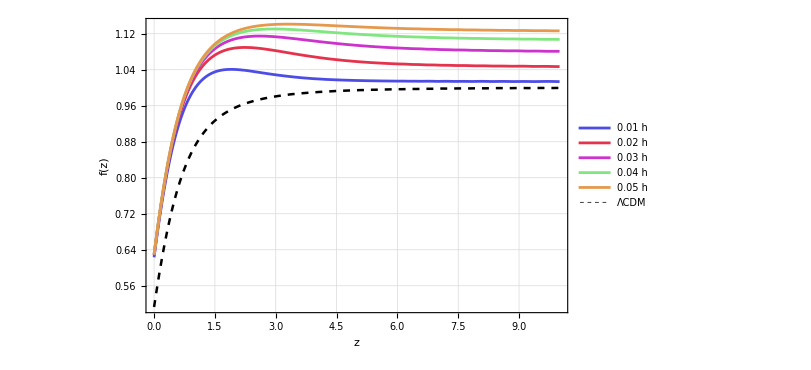

```mathematica
f3Plot=Plot[
{Evaluate[Table[f3[kval,z],{kval,kvals}]], fLCDM[z]},{z,0,10},PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],FrameLabel->{"z","f(z)"},PlotRange->All,Frame->True,ImageSize->600,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed], PlotRangePadding->{None, Scaled[.05]}]

Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model3/f3Plot.png",f0Plot];
```

#### Best fitting modules:

```mathematica
zf=z0;
```

```mathematica
chiSquare[fFunc_,omegaFunc_,gamma_,zMax_,dz_]:=Module[{zVals,data},zVals=Range[0,zMax,dz];
data=Table[(fFunc[z]-omegaFunc[z]^gamma)^2,{z,zVals}];
Total[data]]
```

```mathematica
chiTable[fFunc_,omegaFunc_, gammaGrid_]:=Table[
{g,chiSquare[fFunc,omegaFunc,g,zf,0.01]},
{g,gammaGrid}]
```

```mathematica
bestGamma[fFunc_,omegaFunc_,chiTable_]:=Module[{minRow,bestG,bestChi,nData,dof},minRow=First@Ordering[chiTable[[All,2]],1];
bestG=chiTable[[minRow,1]];
bestChi=chiTable[[minRow,2]];
nData=Length[Range[0,zf,0.01]];(*number of z points,matching chiSquare*)
dof=nData-1;
<|"gamma"->bestG,"chiSq"->bestChi,"dof"->dof,"chiSqReduced"->bestChi/dof|>]
```

```mathematica
approxGamma[fFunc_,omegaFunc_,gi_,zMax_,dz_]:=Module[{result,bestG,bestChi,nData,dof},result=Quiet@FindMinimum[chiSquare[fFunc,omegaFunc,g,zMax,dz],{g,gi}];
bestG=g/. result[[2]];
bestChi=result[[1]];
nData=Length[Range[0,zMax,dz]];
dof=nData-1;
<|"gamma"->bestG,"chiSq"->bestChi,"dof"->dof,"chiSqReduced"->bestChi/dof|>]
```

#### Determine Ωmatter:

```mathematica
Ωmatter[z_] =Ωm0/h[z]^2(1+z)^3;
```

```mathematica
Ωmatter0[z_]:=Ωmatter[z]/.{h->sol0["h"]};
Ωmatter1[z_]:=Ωmatter[z]/.{h->sol1["h"]};
Ωmatter2[z_]:=Ωmatter[z]/.{h->sol2["h"]};
Ωmatter3[z_]:=Ωmatter[z]/.{h->sol3["h"]};
```

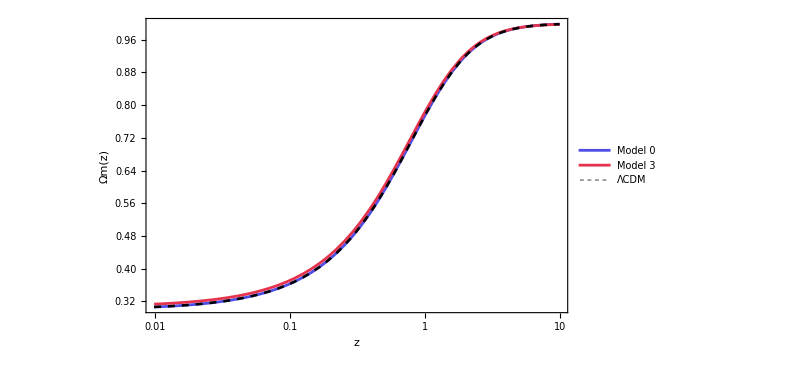

```mathematica
OmatterPlot=LogLinearPlot[
{Ωmatter0[z],Ωmatter3[z], ΩLCDM[z]},{z,0,10},PlotStyle->Append[{RGBColor[0.3,0.3,0.9],RGBColor[0.9,0.2,0.3]},Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[{"Model 0","Model 3","ΛCDM"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],FrameLabel->{"z","Ωm(z)"},
PlotRange->All,Frame->True,ImageSize->600,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed], PlotRangePadding->{None, Scaled[.05]}]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Background solutions/OmatterPlot.png",OmatterPlot];
```

#### Best fit for LCDM

```mathematica
approxgammaLCDM=approxGamma[fLCDM,ΩLCDM,0.5,zf,0.01]
```

<|gamma→0.550468,chiSq→0.000174672,dof→600,chiSqReduced→2.91119×10^-7|>

```mathematica
gammaGridLCDM=Range[0.4,0.6,0.001];
chiTableLCDM=chiTable[fLCDM,ΩLCDM, gammaGridLCDM];
```

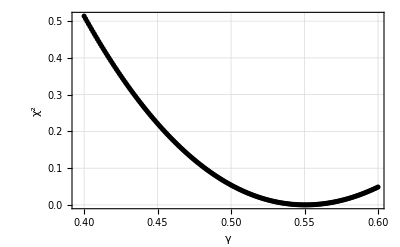

```mathematica
(*Plot chi-square curve to check it's well-behaved (single minimum)*)chiSqPlotLCDM = ListPlot[chiTableLCDM,PlotRange->All,AxesLabel->{"γ","χ^2"},
PlotStyle->Black,
GridLines->Automatic,
Frame->True]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/GrowthIndexApprox/chiSqPlotLCDM.png",chiSqPlotLCDM];
```

```mathematica
resultLCDM=bestGamma[fLCDM,ΩLCDM,chiTableLCDM]
```

<|gamma→0.55,chiSq→0.000179146,dof→600,chiSqReduced→2.98577×10^-7|>

```mathematica
approxgammaLCDM
```

<|gamma→0.550468,chiSq→0.000174672,dof→600,chiSqReduced→2.91119×10^-7|>

```mathematica
gammaLCDM=approxgammaLCDM["gamma"];
```

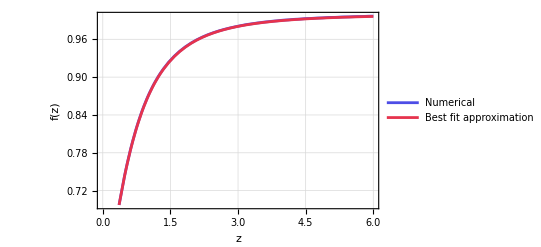

```mathematica
numVsApproxLCDM=Plot[{fLCDM[z],ΩLCDM[z]^gammaLCDM},{z,0,zf},
PlotStyle->colour,
PlotLegends->Placed[
LineLegend[{"Numerical","Best fit approximation"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.7,0.25}],
GridLines->Automatic,
Frame->True,
FrameLabel->{"z","f(z)"}
]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/GrowthIndexApprox/numVsApproxLCDM.png",numVsApproxLCDM];
```

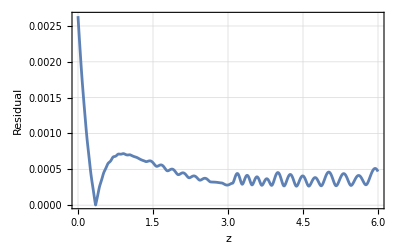

```mathematica
residual[z_]:=fLCDM[z]-ΩLCDM[z]^gammaLCDM
resPlotLCDM=Plot[Abs[residual[z]],{z,0,zf},Frame->True,FrameLabel->{"z","Residual"}, PlotRangePadding->None,
GridLines->Automatic]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/GrowthIndexApprox/resPlotLCDM.png",resPlotLCDM];
```

#### Best fit for model 0

```mathematica
(*Find best gamma for each k value*)
gammaResults0=Association[Table[kval->approxGamma[f0[kval,#]&,Ωmatter0,0.5,zf,0.01],{kval,kvals}]];
```

```mathematica
(*Compute chi tables and best gamma for each k*)
gammaGrid=Range[0.1,0.3,0.01];
gammaResultsBest0=Association[Table[kval->bestGamma[f0[kval,#]&,Ωmatter0,chiTable[f0[kval,#]&,Ωmatter0,gammaGrid]],{kval,kvals}]]
```

<|0.01 h→<|gamma→0.25,chiSq→4.94267,dof→600,chiSqReduced→0.00823778|>,0.02 h→<|gamma→0.21,chiSq→7.48081,dof→600,chiSqReduced→0.012468|>,0.03 h→<|gamma→0.19,chiSq→9.77956,dof→600,chiSqReduced→0.0162993|>,0.04 h→<|gamma→0.18,chiSq→11.6369,dof→600,chiSqReduced→0.0193948|>,0.05 h→<|gamma→0.18,chiSq→13.0682,dof→600,chiSqReduced→0.0217804|>|>

```mathematica
(*Display gamma values in a table*)Grid[Prepend[Table[{NumberForm[N[kval],{4,3}],gammaResults0[kval]["gamma"],gammaResults0[kval]["chiSqReduced"]},{kval,kvals}],{"k (/Mpc)","γ","χ^2/ν"}],Frame->All,FrameStyle->LightGray,Alignment->Center]
```

k (/Mpc) | γ | χ^2/ν
0.010 h | 0.245685 | 0.00823676
0.020 h | 0.207515 | 0.0124677
0.030 h | 0.192374 | 0.0162989
0.040 h | 0.184357 | 0.0193936
0.050 h | 0.179527 | 0.0217804

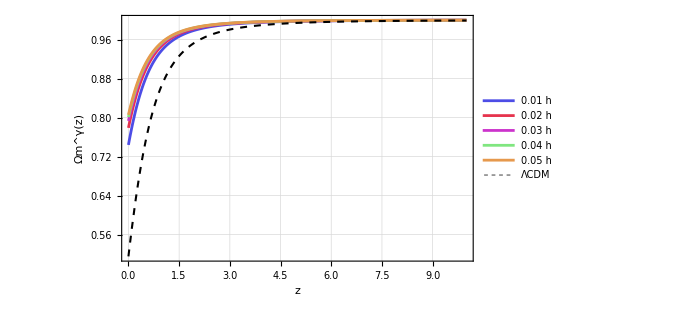

```mathematica
growthIndexApproxPlot0=Plot[
{Evaluate[Table[Ωmatter0[z]^(gammaResults0[kval]["gamma"]),{kval,kvals}]],ΩLCDM[z]^gammaLCDM},{z,0,10},
PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],FrameLabel->{"z","\!\(\*SuperscriptBox[\(Ωm\), \(γ\)]\)(z)"},Frame->True,ImageSize->500,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed], PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model0/growthIndexApproxPlot.png",growthIndexApproxPlot0];
```

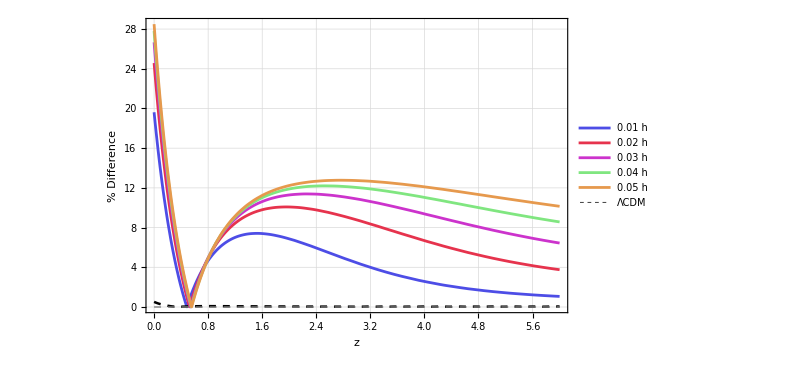

```mathematica
gammaPercentPlot0=
Plot[
{Evaluate[Table[100*Abs[f0[kval,z]-Ωmatter0[z]^(gammaResults0[kval]["gamma"])]/f0[kval,z],{kval,kvals}]],100*Abs[fLCDM[z]-ΩLCDM[z]^gammaLCDM]/fLCDM[z]},{z,0,z0},PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],
PlotRange->All,PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],FrameLabel->{"z","% Difference"},Epilog->{Dashed,Gray,Line[{{0,0},{z0,0}}]},PlotRangePadding->{{0,0},{Scaled[0.05],Scaled[0.05]}},Frame->True,ImageSize->600,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model0/gammaPercentPlot.png",gammaPercentPlot0];
```

#### Best fit for model 3

```mathematica
(*Find best gamma for each k value*)
gammaResults3=Association[Table[kval->approxGamma[f3[kval,#]&,Ωmatter3,0.5,zf,0.01],{kval,kvals}]];
```

```mathematica
(*Compute chi tables and best gamma for each k*)
gammaGrid=Range[0.1,0.3,0.01];
gammaResultsBest3=Association[Table[kval->bestGamma[f3[kval,#]&,Ωmatter3,chiTable[f3[kval,#]&,Ωmatter3,gammaGrid]],{kval,kvals}]]
```

<|0.01 h→<|gamma→0.26,chiSq→4.66358,dof→600,chiSqReduced→0.00777264|>,0.02 h→<|gamma→0.21,chiSq→7.44757,dof→600,chiSqReduced→0.0124126|>,0.03 h→<|gamma→0.19,chiSq→10.2303,dof→600,chiSqReduced→0.0170504|>,0.04 h→<|gamma→0.18,chiSq→12.407,dof→600,chiSqReduced→0.0206783|>,0.05 h→<|gamma→0.18,chiSq→13.9644,dof→600,chiSqReduced→0.0232741|>|>

```mathematica
(*Display gamma values in a table*)Grid[Prepend[Table[{NumberForm[N[kval],{4,3}],gammaResults0[kval]["gamma"],gammaResults0[kval]["chiSqReduced"]},{kval,kvals}],{"k (/Mpc)","γ","χ^2/ν"}],Frame->All,FrameStyle->LightGray,Alignment->Center]
```

k (/Mpc) | γ | χ^2/ν
0.010 h | 0.245685 | 0.00823676
0.020 h | 0.207515 | 0.0124677
0.030 h | 0.192374 | 0.0162989
0.040 h | 0.184357 | 0.0193936
0.050 h | 0.179527 | 0.0217804

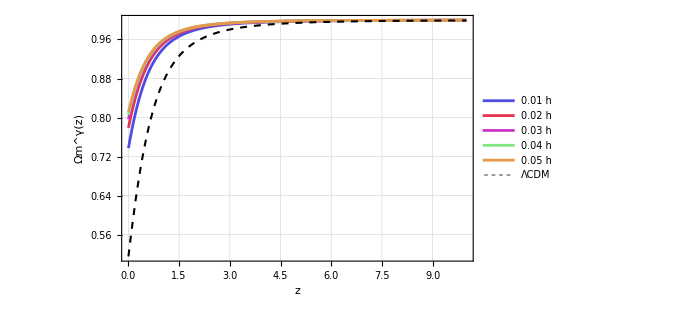

```mathematica
growthIndexApproxPlot3=Plot[
{Evaluate[Table[Ωmatter3[z]^(gammaResults3[kval]["gamma"]),{kval,kvals}]],ΩLCDM[z]^gammaLCDM},{z,0,10},
PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],FrameLabel->{"z","\!\(\*SuperscriptBox[\(Ωm\), \(γ\)]\)(z)"},Frame->True,ImageSize->500,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed], PlotRange->All, PlotRangePadding->{None, Scaled[.05]}]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model3/growthIndexApproxPlot.png",growthIndexApproxPlot3];
```

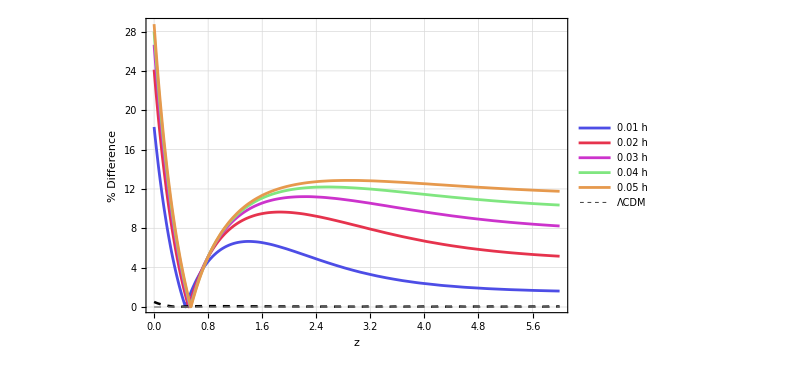

```mathematica
gammaPercentPlot3=
Plot[
{Evaluate[Table[100*Abs[f3[kval,z]-Ωmatter3[z]^(gammaResults3[kval]["gamma"])]/f3[kval,z],{kval,kvals}]],100*Abs[fLCDM[z]-ΩLCDM[z]^gammaLCDM]/fLCDM[z]},{z,0,z0},PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],
PlotRange->All,PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],FrameLabel->{"z","% Difference"},Epilog->{Dashed,Gray,Line[{{0,0},{z0,0}}]},PlotRangePadding->{{0,0},{Scaled[0.05],Scaled[0.05]}},Frame->True,ImageSize->600,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model3/gammaPercentPlot.png",gammaPercentPlot3];
```

### Exact γ factor:

```mathematica
(*γ[z_]= Log[ΩLCDM[z]]/Log[f[z]/.δ->pertDensitySolutions[[1,0]]]*)
γ[z_]= Log[f[z]]/Log[Ωm[z]];
```

```mathematica
γ0[kval_, z_] := γ[z]/.{Ωm->Ωmatter0, δ->pertSols0[kval]["δ"]} ;
γ3[kval_, z_] := γ[z]/.{Ωm->Ωmatter3, δ->pertSols3[kval]["δ"]} ;
γLCDM[z_] = γ[z]/.{Ωm->ΩLCDM, δ->LCDMsol[[1,2]]} ;
```

```mathematica
f[z]
```

((-1-z) δ'[z])/δ[z]

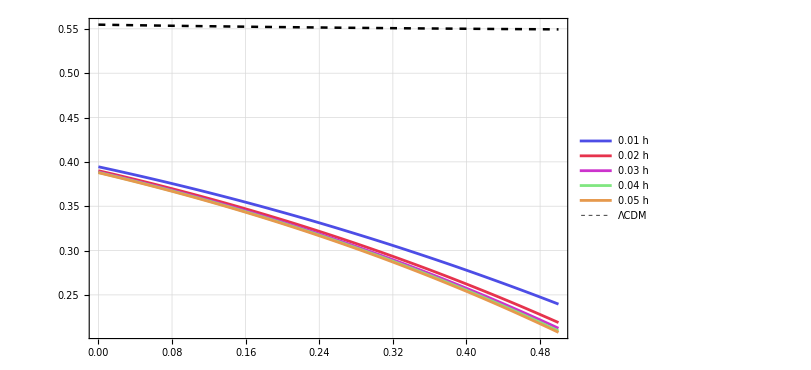

```mathematica
gamma0=Plot[{Evaluate[Table[γ0[kval, z],{kval,kvals}]],γLCDM[z]},{z,0,0.5},PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],Frame->True,ImageSize->600,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model0/gamma.png",gamma0];
```

```mathematica
N[6/11]
```

0.545455

```mathematica
γLCDM[0]
```

0.554729

```mathematica
γ0[0.01h,0]
```

0.394473

```mathematica
γ3[0.01h,0]
```

0.40024

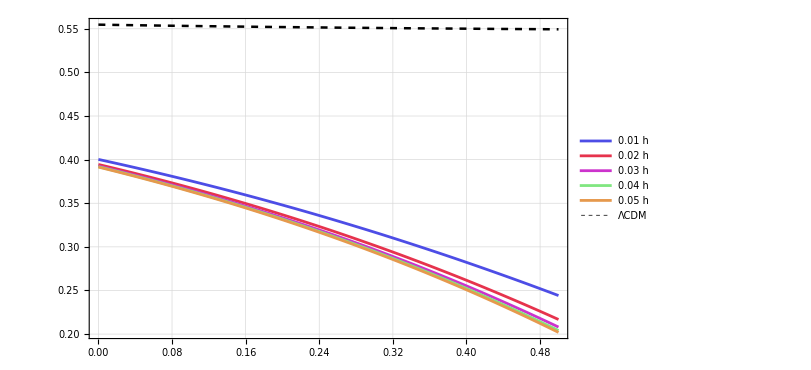

```mathematica
gamma3=Plot[{Evaluate[Table[γ3[kval, z],{kval,kvals}]],γLCDM[z]},{z,0,0.5},PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],Frame->True,ImageSize->600,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/Model3/gamma.png",gamma3];
```

```mathematica
TableForm[Table[{k,γ0[k,0],γ3[k,0]},{k,kvals}],TableHeadings->{None,{"k","γ0(z=0)","γ3(z=0)"}}]
```

k | γ0(z=0) | γ3(z=0)
0.01 h | 0.394473 | 0.40024
0.02 h | 0.390033 | 0.394448
0.03 h | 0.38871 | 0.392682
0.04 h | 0.388101 | 0.391884
0.05 h | 0.387764 | 0.391464

### Plotting fσ8

```mathematica
(*σ8[z_]= σ80 δ[z]/δ[0];*)
σ80=0.77;
```

```mathematica
fσ8[z_]=-(σ80 (1+z) δ'[z])/δ[0];
```

```mathematica
fσ8[z]
```

-(0.77 (1+z) δ'[z])/δ[0]

```mathematica
fσ80[kval_,z_]:=fσ8[z]/.{δ->pertSols0[kval]["δ"][z]};
fσ8LCDM[z_]:=fσ8[z]/.{δ->LCDMsol[[1,2]]};
```

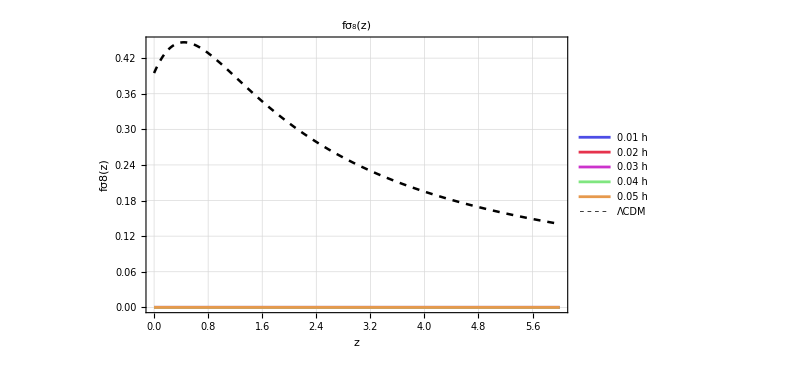

```mathematica
fSigma8Plot0=Plot[{Evaluate[Table[fσ80[kval,z],{kval,kvals}]],fσ8LCDM[z]},{z,0,z0},PlotStyle->Append[colour,Directive[Black,Dashed,Thickness[0.003]]],PlotLegends->Placed[LineLegend[Join[N[kvals],{"ΛCDM"}],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.88,0.3}],FrameLabel->{"z","fσ8(z)"},PlotLabel->"f\!\(\*SubscriptBox[\(σ\), \(8\)]\)(z)",PlotRangePadding->{{0,0},{Scaled[0.05],Scaled[0.05]}},Frame->True,ImageSize->600,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/fsigma8plot.png",fσ8LogPlot];
```

### Reading in fσ_8 data:

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/Cosmological perturbations"];
data=Rest@Import["fsigma8.txt","Table"];
data=Select[data,Length[#]>=2&];
```

```mathematica
obsData=Table[{{data[[i,1]],data[[i,2]]},ErrorBar[data[[i,3]]]},{i,Length[data]}];
```

```mathematica
obsPlot=ErrorListPlot[obsData,PlotStyle->{Black,PointSize[0.01], Thickness[0.003]}, PlotRange->{0,1}];
```

```mathematica
fσ8Plot=
Plot[{fσ80[z],fσ81[z],fσ82[z],fσ83[z],fσ8LCDM[z]},{z,2.5,0},PlotRange->All,PlotLegends->Placed[
LineLegend[{"Model 0","ΛCDM"},
LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],
{0.85,0.7}],
FrameLabel->{"z","fσ_8(z)"},PlotStyle->colour,PlotRangePadding->{{0,0},{Scaled[0.05],Scaled[0.05]}},Frame->True,ImageSize->500,
GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]];
```

Show::gcomb: Could not combine the graphics objects in Show[,ErrorListPlot[{{{0.35,0.44},ErrorBar[0.05]},{{0.77,0.49},ErrorBar[0.18]},{{0.17,0.51},ErrorBar[0.06]},{{0.02,0.314},ErrorBar[0.048]},{{0.02,0.398},ErrorBar[0.065]},{{0.25,0.3512},ErrorBar[0.0583]},{{0.37,0.4602},ErrorBar[0.0378]},{{0.25,0.3665},ErrorBar[0.0601]},{{0.37,0.4031},ErrorBar[0.0586]},{{0.44,0.413},ErrorBar[0.08]},«56»},«9»→«1»,PlotRange→{0,1}]].

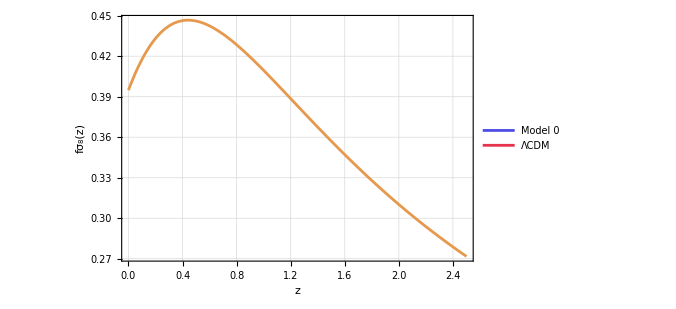
Show[-Graphics-,ErrorListPlot[{{{0.35,0.44},ErrorBar[0.05]},{{0.77,0.49},ErrorBar[0.18]},{{0.17,0.51},ErrorBar[0.06]},{{0.02,0.314},ErrorBar[0.048]},{{0.02,0.398},ErrorBar[0.065]},{{0.25,0.3512},ErrorBar[0.0583]},{{0.37,0.4602},ErrorBar[0.0378]},{{0.25,0.3665},ErrorBar[0.0601]},{{0.37,0.4031},ErrorBar[0.0586]},{{0.44,0.413},ErrorBar[0.08]},{{0.6,0.39},ErrorBar[0.063]},{{0.73,0.437},ErrorBar[0.072]},{{0.06,0.423},ErrorBar[0.055]},{{0.3,0.407},ErrorBar[0.055]},{{0.4,0.419},ErrorBar[0.041]},{{0.5,0.427},ErrorBar[0.043]},{{0.6,0.433},ErrorBar[0.067]},{{0.8,0.47},ErrorBar[0.08]},{{0.35,0.429},ErrorBar[0.089]},{{0.18,0.36},ErrorBar[0.09]},{{0.38,0.44},ErrorBar[0.06]},{{0.32,0.384},ErrorBar[0.095]},{{0.32,0.48},ErrorBar[0.1]},{{0.57,0.417},ErrorBar[0.045]},{{0.15,0.49},ErrorBar[0.145]},{{0.1,0.37},ErrorBar[0.13]},{{1.4,0.482},ErrorBar[0.116]},{{0.59,0.488},ErrorBar[0.06]},{{0.38,0.497},ErrorBar[0.045]},{{0.51,0.458},ErrorBar[0.038]},{{0.61,0.436},ErrorBar[0.034]},{{0.38,0.477},ErrorBar[0.051]},{{0.51,0.453},ErrorBar[0.05]},{{0.61,0.41},ErrorBar[0.044]},{{0.76,0.44},ErrorBar[0.04]},{{1.05,0.28},ErrorBar[0.08]},{{0.32,0.427},ErrorBar[0.056]},{{0.57,0.426},ErrorBar[0.029]},{{0.727,0.296},ErrorBar[0.0765]},{{0.02,0.428},ErrorBar[0.0465]},{{0.6,0.55},ErrorBar[0.12]},{{0.86,0.4},ErrorBar[0.11]},{{0.1,0.48},ErrorBar[0.16]},{{0.001,0.505},ErrorBar[0.085]},{{0.85,0.45},ErrorBar[0.11]},{{0.31,0.384},ErrorBar[0.083]},{{0.36,0.409},ErrorBar[0.098]},{{0.4,0.461},ErrorBar[0.086]},{{0.44,0.426},ErrorBar[0.062]},{{0.48,0.458},ErrorBar[0.063]},{{0.52,0.483},ErrorBar[0.075]},{{0.56,0.452},ErrorBar[0.063]},{{0.59,0.452},ErrorBar[0.061]},{{0.64,0.379},ErrorBar[0.054]},{{0.1,0.376},ErrorBar[0.038]},{{1.52,0.42},ErrorBar[0.076]},{{1.52,0.396},ErrorBar[0.079]},{{0.978,0.379},ErrorBar[0.176]},{{1.23,0.385},ErrorBar[0.099]},{{1.526,0.342},ErrorBar[0.07]},{{1.944,0.364},ErrorBar[0.106]},{{0.6,0.49},ErrorBar[0.12]},{{0.86,0.46},ErrorBar[0.09]},{{0.57,0.501},ErrorBar[0.051]},{{0.03,0.404},ErrorBar[0.0815]},{{0.72,0.454},ErrorBar[0.139]}},PlotStyle→{GrayLevel[0],PointSize[0.01],Thickness[0.003]},PlotRange→{0,1}]]

```mathematica
fσ8DataPlot=Show[fσ8Plot, obsPlot]
Export["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Report/f(R) figures/Perturbations/fsigma8Dataplot.png",fσ8DataPlot];
```